This program finds the region of absolute stability for Question 3(d). It confirms the results found by hand. The region of absolute stability can be found by solving Π(z,H) = ρ(z) - H σ(z) = 0. ρ(z) and σ(z) are the characteristic polynomials of the multistep method. H is defined using the model problem y’(t) = λ y(t), with λ < 0 and y(0) = y_0. H = λ h and H < 0 by definition.

```mathematica
(*Characteristic polynomials of the multi-step method*)
ρ=z^2-z;
σ=5/12z^2+2/3z-1/12;

(*Finding roots of Π(z,H)*)
sol=Solve[ρ-H(σ)==0,z];
z1=z/.sol[[1]];
z2=z/.sol[[2]];

(*Finding region of absolute stability in terms of H = λ h*)
Reduce[-1<z1<1&&-1<z2<1&&H<0,H]
```

-6<H<0

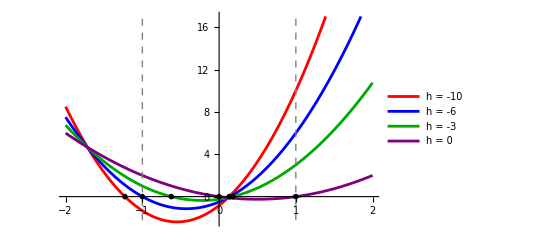

```mathematica
(*Showing results graphically*)
(*Finding solutions of the characteristic polynomial Π for H = -10, -6, -3, 0.*)
sol10 = Solve[ρ+10σ==0,z];
sol6 = Solve[ρ+6σ==0,z];
sol3 = Solve[ρ+3σ==0,z];
sol0 = Solve[ρ-0 σ==0,z];

(*Plotting Π for H = -10, -6, -3, 0 and the roots of Π=0 in each case. As can be seen, if H is not in -6 < H < 0, i.e. for H = -10, at least one root lies out of the range [-1,1]*)
roots=Graphics[{PointSize[0.01],{{Black,Point[{z/.sol10[[1]],0}]}},{Black,Point[{z/.sol10[[2]],0}]},{{Black,Point[{z/.sol6[[1]],0}]}},{{Black,Point[{z/.sol6[[2]],0}]}},{{Black,Point[{z/.sol3[[1]],0}]}},{{Black,Point[{z/.sol3[[2]],0}]}},{{Black,Point[{z/.sol0[[1]],0}]}},{{Black,Point[{z/.sol0[[2]],0}]}}}];
plot =Plot[{ρ+10σ,ρ+6σ,ρ+3σ,ρ-0σ},{z,-2,2},PlotStyle->{Red,Blue,Darker[Green],Purple},PlotLegends->{"h = -10", "h = -6", "h = -3", "h = 0"},Epilog->{{Dashed,Gray,Line[{{1,-5},{1,20}}]},{Dashed,Gray,Line[{{-1,-5},{-1,20}}]}}];
Show[plot,roots]
```